```mathematica
Clear["Global`*"]
```

# Alternative Ansatz

## Cory Aitchison - February 2022

Consider another ansatz

## Set Up

### Miscellaneous

```mathematica
CC[x_]:=Cos[σ x] / Cosh[σ x];
SS[x_]:=Sin[σ x] / Sinh[σ x];
LDE[f_]:=D[f[x],{x,4}] + 4 σ^4 f[x] ;
NDE[f_]:=Γ f[x]^3;
letters = {c, d, e, f, g, h, i, j, k};
```

### Ansatz

```mathematica
u[n_]:=x|->Sum[letters[[n]][i]CC[x]^((2n+1)-i) SS[x]^(i), {i, 0, 2n+1}];
u[0] := x |->A CC[x] + B SS[x];
```

```mathematica
<<"/Users/cory/Sync/USYD/Denison/Mathematica/PQSHelper.wl"
```

### Solutions

```mathematica
SubAnswers[eq_, n_] := SubAnswers[eq /. answer[n-1], n-1];
SubAnswers[eq_, 1] := eq;

GetEquation[n_]:= LDE[x |-> Sum[u[k][x], {k, 0, n}]] + NDE[x |-> Sum[u[k][x], {k, 0, n-1}]];
GetSolution[n_] := AnalyticSolve[SubAnswers[GetEquation[n], n], n, x, σ, letters[[n]]] // FullSimplify;

GetLinear[ans_] := Coefficient[(Last /@List @@@ ans)/. B->0 ,A, 1]A + Coefficient[(Last /@List @@@ ans)/. A->0 ,B, 1]B;
ShowLinear[n_]:=(x |-> PadRight[x, 2 + 2n,  _])/@GetLinear/@ (answer[#]&/@Range[1,n]) // Transpose// MatrixForm ;

ShowValues[n_] := (x |-> PadRight[x, 2 + 2n, _])/@((answer[#]/. param /. estimates)&/@Range[1,n])//Transpose//MatrixForm;

FinalFunction[n_] := SubAnswers[Sum[u[k][x], {k, 0, n}], n+1]/.param  /. estimates;
FinalFunction[0] := u[0][x] /. param /. estimates;
```

### Numerical Values

```mathematica
param = {σ-> 6^(1/4), Γ -> -24};
estimates = {A -> 0.445408, B -> 1.02817};
taylorests[0] = {A->0.033327514775158475,B->1.153359200278144};
taylorests[1] = {A->0.24242264239512362,B->0.8985343791605391};
taylorests[3] = {A->0.33494186742400267,B->0.6945601303275413};
```

```mathematica
DumpGet["/Users/cory/Sync/USYD/Denison/Mathematica/answerSave.mx"]
```

### Long data

```mathematica
data = Import["/Users/cory/Sync/USYD/Denison/MATLAB/PQS analytic/PureQuartic.csv"];
```

```mathematica
fdata = Interpolation[data];
fdata4[x_] := 4σ^4 fdata[x]+ Γ fdata[x]^3 /. param;
```

## Ansatz

```mathematica
(*g[0]= x|-> Cos[σ x](a Exp[σ x] + b Exp[-σ x]) + Sin[σ x](c Exp[σ x] + d Exp[-σ x]);*)
g[0]= x|-> Piecewise[{{Exp[-σ x] (a[1] Cos[σ x] + a[2]Sin[σ x]), x > 0}, {Exp[σ x](a[1] Cos[σ x] - a[2]Sin[σ x]), x <= 0}}];
```

```mathematica
g[0][x]
```

Piecewise[{{ⅇ^(-x σ) (a[1] Cos[x σ]+a[2] Sin[x σ]), x>0}, {ⅇ^(x σ) (a[1] Cos[x σ]-a[2] Sin[x σ]), x≤0}, {0, True}}]

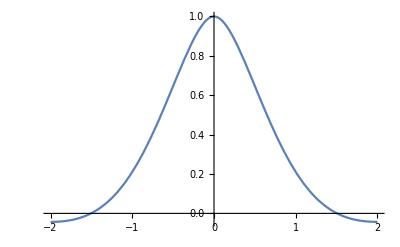

```mathematica
Plot[g[0][x] /. param /. {a[1] -> 1, a[2] -> 1}, {x,-2,2}]
```

```mathematica
LDE@g[0] // FullSimplify
```

Piecewise[{{0, x≠0}, {Indeterminate, True}}]

```mathematica
g[1]=  x|-> Piecewise[{{Exp[-3σ x] (b[1] Cos[3σ x] + b[2] Cos[σ x]), x > 0}, {Exp[3σ x](b[1] Cos[3σ x] + b[2] Cos[σ x]), x <= 0}}];
```

```mathematica
g[1][x]
```

Piecewise[{{ⅇ^(-3 x σ) (b[2] Cos[x σ]+b[1] Cos[3 x σ]), x>0}, {ⅇ^(3 x σ) (b[2] Cos[x σ]+b[1] Cos[3 x σ]), x≤0}, {0, True}}]

```mathematica
LDE[x |-> g[0][x] + g[1][x]] + NDE[g[0]] // FullSimplify
```

Piecewise[{{ⅇ^(3 x σ) (32 σ^4 b[2] Cos[x σ]+a^3 Γ Cos[x σ]^3-32 σ^4 (10 b[1] Cos[3 x σ]+3 b[2] Sin[x σ])), x<0}, {ⅇ^(-3 x σ) (32 σ^4 b[2] Cos[x σ]+a^3 Γ Cos[x σ]^3+32 σ^4 (-10 b[1] Cos[3 x σ]+3 b[2] Sin[x σ])), x>0}, {Indeterminate, True}}]

```mathematica
g[2]= t |-> %113 /. x -> t;
```

```mathematica
Manipulate[Show[Plot[g[0][x] + g[1][x] /. param /. {a-> aa, b -> bb}, {x,-4,4}], ListLinePlot[data, PlotStyle->{Gray, Dashed}, PlotRange->{{-4,4},All}]], {aa, 0, 6}, {bb,0,2}]
```

ReplaceAll::reps: {param} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ListLinePlot::lpn: data is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[,ListLinePlot[data,PlotStyle→{GrayLevel[0.5],Dashing[{Small,Small}]},PlotRange→{{-4,4},All}]].